```mathematica
NS["mctests1","C:\\Users\\pglpm\\repositories\\maxNt\\scripts"]
```

```mathematica
me=Flatten@Import["stensola2_6mom_prior2_N1000.csv"];
```

```mathematica
file="testmc_c6_p1_samplesf_N1000_L500_s300_a1e+06";
```

```mathematica
samplesb=Import[file<>".csv"];dd=Dimensions[samplesb];
{nn=dd[[2]]-1,ss=dd[[1]]}
```

{1000,300}

```mathematica
av=Mean[samplesb];
md=Quantile[samplesb,1/2];q1=Quantile[samplesb,16/100];q2=Quantile[samplesb,84/100];
```

```mathematica
samp=10;samplesb2=Join[samplesb[[Round@Subdivide[1,ss,samp-1]]],{av,md,q1,q2,me}];
```

```mathematica
plot=ListPlot[samplesb2*nn,Joined->True,PlotStyle->Join[Table[{solid,Black,Thin,Opacity[0.75]},samp],{{solid,blue,Thick},{solid,green,Thick},{solid,yellow,Thick},{solid,yellow,Thick},{solid,red,Thick}}],DataRange->{0,1},PlotRange->{{All,0.05},{All,120}}];
expdf[file,plot];
```

```mathematica
plot=ListPlot[samplesb2[[250]]*nn,Joined->True,PlotStyle->Join[Table[{solid,Black,Thick,Opacity[1]},ss],{{solid,green,Thick},{solid,red,Thick},{solid,yellow,Thick},{solid,yellow,Thick},{solid,blue,Thick}}],DataRange->{0,1},PlotRange->{{All,0.05},{All,All}}];
expdf["ex"<>file,plot];
```

```mathematica
listdiff=Total[Differences[#,4]^2]&/@samplesb;
listdiffx=Total[Differences[#,4]^2]&/@{av,md,me}
```

{8.87641×10^-6,0.0157514,7.99029×10^-6}

```mathematica
{Mean[listdiff],Max@listdiff}
```

{0.000982577,0.0137769}

```mathematica
h[x_]:=Total[Block[{Indeterminate=0},-x*Log[x]]];
```

```mathematica
listh=h/@samplesb;
listhx=h/@{av,md,me}
```

{3.50464,3.37751,3.34491}

```mathematica
{Mean[listh],Max@listh}
```

{3.40961,3.50147}

```mathematica
listz=Count[#,0]&/@samplesb;
```

```mathematica
(* check other variable *)
```

```mathematica
xsamp=Import["testmc_c6_p1_samplesx_N1000_L500_s300_a1e+06.csv"];
```

```mathematica
ListPointPlot3D[{xsamp[[;;,;;3]],xsamp[[;;,499;;501]],xsamp[[;;,-3;;]]},PlotStyle->Directive[Opacity[0.5]],PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->1,Axes->True,AxesLabel->{1,2,3}]
```

-Graphics3D-

```mathematica
xsamp=Import["testmc_r_c6_p1_samplesx_N1000_L500_s300_a1e+06.csv"];
```

```mathematica
ListPointPlot3D[{xsamp[[;;,;;3]],xsamp[[;;,499;;501]],xsamp[[;;,-3;;]]},PlotStyle->Directive[Opacity[0.5]],PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->1,Axes->True,AxesLabel->{1,2,3}]
```

-Graphics3D-

```mathematica
(* prior *)
```

```mathematica
filep="pre_x4testmc_p1_samplesf_N2000_L10_s300_a20000";
```

```mathematica
samplesp=Import[filep<>".csv"];dd=Dimensions[samplesp];
{nn=dd[[2]]-1,ss=dd[[1]]}
```

{2000,300}

```mathematica
av=Mean[samplesp];
md=Quantile[samplesp,1/2];q1=Quantile[samplesp,16/100];q2=Quantile[samplesp,84/100];
```

```mathematica
samplesp2=Join[samplesp,{av,md,q1,q2}];
```

```mathematica
plot=ListPlot[samplesp2*nn,Joined->True,PlotStyle->Join[Table[{solid,Black,Thin,Opacity[0.1]},ss],{{solid,green,Thick},{solid,red,Thick},{solid,yellow,Thick},{solid,yellow,Thick}}],DataRange->{0,1},PlotRange->{{All,0.05},{All,All}}];
expdf[filep,plot];
```

```mathematica
ListPlot[samplesb2,Joined->True,PlotStyle->Join[Table[{solid,Black,Thin,Opacity[0.1]},ss],{{solid,red,Thick},{solid,yellow,Thick},{solid,yellow,Thick},{solid,blue,Thick}}],DataRange->{0,1},PlotRange->{{All,0.05},{All,All}}]
```

```mathematica
samplesb=Import["x4testmcsamplesf_N1000_L50_s300_a10000.csv"];Dimensions[samplesb]
```

{300,1001}

```mathematica
nn=Dimensions[samplesb][[2]]-1;ss=Dimensions[samplesb][[1]]
```

300

```mathematica
md=Quantile[samplesb,1/2];q1=Quantile[samplesb,1/4];q2=Quantile[samplesb,3/4];
```

```mathematica
me=Flatten@Import["stensola2_6mom_prior2_N1000.csv"];
```

```mathematica
samplesb2=Join[samplesb,{md,q1,q2,me}];
```

```mathematica
ListPlot[samplesb2,Joined->True,PlotStyle->Join[Table[{solid,Black,Thin,Opacity[0.1]},ss],{{solid,red,Thick},{solid,yellow,Thick},{solid,yellow,Thick},{solid,blue,Thick}}],DataRange->{0,1},PlotRange->{{All,0.05},{All,All}}]
```

```mathematica
samples=Import["x4testmccontrsamplesf_N1000_L50_s300_a10000.csv"];Dimensions[samples]
```

{300,1001}

```mathematica
nn=Dimensions[samples][[2]]-1;ss=Dimensions[samples][[1]]
```

300

```mathematica
md=Quantile[samples,1/2];q1=Quantile[samples,1/4];q2=Quantile[samples,3/4];
```

```mathematica
samples2=Join[samples,{md,q1,q2}];
```

```mathematica
ListPlot[samples2,Joined->True,PlotStyle->Join[Table[{solid,Black,Thin,Opacity[0.1]},ss],{{solid,red,Thick},{solid,yellow,Thick},{solid,yellow,Thick}}],DataRange->{0,1},PlotRange->{{All,0.05},{All,Auto}}]
```

```mathematica
samples=Import["x4testmccontrsamplesf_N1000_L10_s300_a1000.csv"];Dimensions[samples]
```

{300,1001}

```mathematica
nn=Dimensions[samples][[2]]-1;ss=Dimensions[samples][[1]]
```

300

```mathematica
md=Quantile[samples,1/2];q1=Quantile[samples,1/4];q2=Quantile[samples,3/4];
```

```mathematica
samples2=Join[samples,{md,q1,q2}];
```

```mathematica
ListPlot[samples2,Joined->True,PlotStyle->Join[Table[{solid,Black,Thin,Opacity[0.1]},ss],{{solid,red,Thick},{solid,yellow,Thick},{solid,yellow,Thick}}],DataRange->{0,1},PlotRange->{{All,0.05},{All,Auto}}]
```

```mathematica
samples2=Append[samples,means=Mean[samples]];
```

```mathematica
ListPlot[samples2,Joined->True,PlotStyle->Append[Table[{solid,Black,Thin,Opacity[0.1]},ss],{solid,red,Thick}],DataRange->{0,1},PlotRange->{{All,0.1},{All,All}}]
```

```mathematica
q1=Quantile[samples,0.25];q2=Quantile[samples,0.75];
```

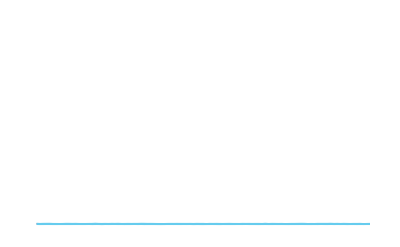

```mathematica
ListPlot[{means,q1,q2},Joined->True,PlotStyle->{{solid,red,Thick},{dashed,blue,Thin},{dashed,blue,Thin}},DataRange->{0,1},PlotRange->{{All,0.1},{All,0.3}}]
```